## Bose-Hubbard model simulation

References:
	F. Verstraete, V. Murg, J. I. Cirac
	Matrix product states, projected entangled pair states, and variational renormalization group methods for quantum spin systems
	Advances in Physics 57, 143-224 (2008) DOI

	Thomas Barthel
	Precise evaluation of thermal response functions by optimized density matrix renormalization group schemes
	New Journal of Physics 15, 073010 (2013) DOI

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<../mathematica/mps_base.m
```

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
SiteCreateOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],-1]
SiteAnnihilOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],1]
```

```mathematica
NumberOp[M_]:=DiagonalMatrix[Range[0,M]]
```

```mathematica
Z[H_,β_]:=Norm[MatrixExp[-β/2 H],"Frobenius"]^2
```

```mathematica
(* construct Bose-Hamiltonian with open boundary conditions *)
Subscript[H, bose][t_,U_,μ_,M_,1]:=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M]
Subscript[H, bose][t_,U_,μ_,M_,L_]:=-t Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]],{l,1,L-1}]+Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SparseIdentityMatrix[(M+1)^(L-l)]],{l,1,L}]
```

### Simulation parameters

```mathematica
(* kinetic hopping parameter *)
Subscript[tH, val]=1;
```

```mathematica
(* interaction strength *)
Subscript[U, val]=5;
```

```mathematica
(* chemical potential *)
Subscript[μ, val]=1/7;
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=5;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
(* inverse temperature *)
Subscript[β, val]=3/5;
```

```mathematica
Subscript[t, list]=Range[0,5,1/4];
Length[%]
```

21

### Compare MPO representation of ⅇ^(-β H/2) with reference calculation

```mathematica
(* local Hamiltonian terms acting on neighboring lattice sites *)
h2[t_,U_,μ_,M_,L_]:=Module[{bd=SiteCreateOp[M],b=SiteAnnihilOp[M],S=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SI,IS},SI=KroneckerProduct[S,IdentityMatrix[M+1]];IS=KroneckerProduct[IdentityMatrix[M+1],S];Table[-t(KroneckerProduct[bd,b]+KroneckerProduct[b,bd])+If[j==1,SI+1/2 IS,If[j<L-1,1/2(SI+IS),1/2 SI+IS]],{j,L-1}]]
```

```mathematica
(* check *)
Block[{t,U,μ,M=2,L=5},Norm[Flatten[FullSimplify[Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],h2[t,U,μ,M,L]⟦l⟧,SparseIdentityMatrix[(M+1)^(L-l-1)]],{l,1,L-1}]-Subscript[H, bose][t,U,μ,M,L]]]]]
```

0

```mathematica
(* MPO representing identity operation *)
MPOId[M_,L_]:=Table[ArrayReshape[IdentityMatrix[M+1],{M+1,M+1,1,1}],{i,L}]
```

```mathematica
(* compute reference MPO representation of ⅇ^(-β H/2) *)
Block[{M=Subscript[M, val],L=Subscript[L, val],Δτ=1/40,β=Subscript[β, val],tol=10^-10},Subscript[A, ρβ,ref]=MPOEvolution[MPOStrangStep,N[MPOId[M,L]],h2[Subscript[tH, val],Subscript[U, val],Subscript[μ, val],M,L],β/2,β/(2Δτ),tol]];
Dimensions/@%
```

{{3,3,1,9},{3,3,9,22},{3,3,22,22},{3,3,22,9},{3,3,9,1}}

```mathematica
(* compare with "exact" ⅇ^(-β H/2) *)
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],ρ,HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];ρ=MatrixExp[-β/2 HB];Norm[MPOMergeFull[Subscript[A, ρβ,ref]]-ρ]/Norm[ρ]]
```

0.000265157

```mathematica
(* example *)
Subscript[A, ρβ,ref]⟦3,2,2,{1,2,-1},{1,2,-1}⟧//MatrixForm
```

(-0.70856 | -1.91756×10^-17 | -1.52739×10^-19
-3.38918×10^-16 | -0.231038 | -5.30961×10^-18
6.61363×10^-15 | -2.93872×10^-13 | -0.00177101)

```mathematica
(* virtual bond dimensions obtained by C implementation *)
Subscript[D, ρβ]=Import["../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"_rho/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>"_D.dat","Integer64"]
```

{1,9,22,22,9,1}

```mathematica
(* read MPO tensors of ⅇ^(-β H/2) from disk *)
Subscript[A, ρβ]=Block[{M=Subscript[M, val],L=Subscript[L, val],D=Subscript[D, ρβ]},Table[Transpose[ArrayReshape[First[#]+ⅈ Last[#]&/@Partition[Import["../output/bose_hubbard/L"<>ToString[L]<>"_rho/bose_hubbard_L"<>ToString[L]<>"_M"<>ToString[M]<>"_A"<>ToString[i]<>".dat","Real64"],2],{D⟦i+2⟧,D⟦i+1⟧,M+1,M+1}],Reverse[Range[4]]],{i,0,L-1}]];
Dimensions/@%
```

{{3,3,1,9},{3,3,9,22},{3,3,22,22},{3,3,22,9},{3,3,9,1}}

```mathematica
(* check normalization *)
Norm[MPOMergeFull[Subscript[A, ρβ]],"Frobenius"]-1
```

6.66134×10^-16

```mathematica
(* compare with reference *)
Block[{ρβref=MPOMergeFull[Subscript[A, ρβ,ref]]},Norm[MPOMergeFull[Subscript[A, ρβ]]-ρβref/Norm[ρβref,"Frobenius"]]]
```

9.9727×10^-15

### Response function

```mathematica
χC[A_,B_,H_,β_,t_]:=Module[{tA=t/2,tB=t/2,ρβ=MatrixExp[-β/2 H]},1/Z[H,β] Tr[(MatrixExp[ⅈ tB H].ρβ.B.MatrixExp[-ⅈ tB H]).(MatrixExp[-ⅈ tA H].A.ρβ.MatrixExp[ⅈ tA H])]]
```

```mathematica
Subscript[A, op][n_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^(n-1)],NumberOp[M],SparseIdentityMatrix[(M+1)^(L-n)]]
```

```mathematica
(* read simulation results from disk *)
Subscript[χ, list]=First[#]+ⅈ Last[#]&/@Partition[Import["../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>"_chi.dat","Real64"],2]
Dimensions[%]
```

{0.455154+0. ⅈ,0.452383+0.00568877 ⅈ,0.465795+0.0215241 ⅈ,0.491346+0.0182174 ⅈ,0.497773+0.00931562 ⅈ,0.50718+0.0163036 ⅈ,0.528373+0.00712758 ⅈ,0.522174-0.0192632 ⅈ,0.491763-0.0261732 ⅈ,0.469013-0.0118098 ⅈ,0.465239+0.0139632 ⅈ,0.490941+0.0467734 ⅈ,0.54984+0.0677079 ⅈ,0.618686+0.0543133 ⅈ,0.65343+0.00469729 ⅈ,0.626502-0.0447879 ⅈ,0.56772-0.0592028 ⅈ,0.514774-0.0493978 ⅈ,0.476244-0.0249369 ⅈ,0.46878+0.0141994 ⅈ,0.502955+0.0479626 ⅈ}

{21}

```mathematica
Subscript[j, A]=2;
Subscript[j, B]=4;
```

```mathematica
(* reference calculation *)
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[χ, list,ref]=Table[χC[N[Subscript[A, op][Subscript[j, A],M,L]],N[Subscript[A, op][Subscript[j, B],M,L]],HB,β,t],{t,Subscript[t, list]}]]
```

{0.45511,0.452337+0.00568806 ⅈ,0.465744+0.021527 ⅈ,0.4913+0.0182227 ⅈ,0.497729+0.00931571 ⅈ,0.507132+0.0163003 ⅈ,0.528321+0.00712611 ⅈ,0.522122-0.0192627 ⅈ,0.491713-0.0261719 ⅈ,0.468961-0.0118075 ⅈ,0.465187+0.0139672 ⅈ,0.490893+0.0467772 ⅈ,0.549796+0.067711 ⅈ,0.618648+0.0543114 ⅈ,0.65339+0.00469154 ⅈ,0.62646-0.0447926 ⅈ,0.567675-0.0592081 ⅈ,0.514723-0.0494027 ⅈ,0.476188-0.0249383 ⅈ,0.468725+0.0142005 ⅈ,0.502905+0.0479636 ⅈ}

```mathematica
(* compare *)
Abs[Subscript[χ, list]-Subscript[χ, list,ref]]
```

{0.0000441544,0.0000466972,0.0000507795,0.0000469138,0.0000440969,0.0000486904,0.0000520062,0.000051623,0.0000509416,0.0000522433,0.0000517793,0.0000488358,0.0000440189,0.0000388544,0.0000404726,0.0000420798,0.0000448069,0.0000514381,0.0000556816,0.0000544809,0.0000504625}

```mathematica
Subscript[plot, label]="Bose-Hubbard model with\nt_H="<>ToString[Subscript[tH, val]]<>", U="<>ToString[Subscript[U, val]]<>", μ="<>ToString[InputForm[Subscript[μ, val]]]<>", M="<>ToString[Subscript[M, val]]<>", L="<>ToString[Subscript[L, val]]<>", β="<>ToString[N[Subscript[β, val]]]<>" (scheme C)\nA: number operator at site "<>ToString[Subscript[j, A]]<>", B: number operator at site "<>ToString[Subscript[j, B]];
```

```mathematica
Subscript[fn, export]="plots/"<>#<>"/"<>#<>"_"&[FileBaseName[NotebookFileName[]]];
```

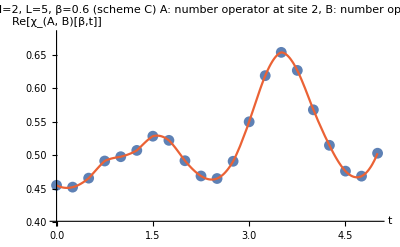

```mathematica
Show[ListPlot[Transpose[{Subscript[t, list],Re[Subscript[χ, list]]}],PlotRange->{Automatic,{0.4,0.68}},AxesLabel->{"t","Re[χ_(A, B)[β,t]]"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation"],Plot[Interpolation[Transpose[{Subscript[t, list],Re[Subscript[χ, list,ref]]}]][τ],{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"chiAB_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

### Virtual bond dimensions

```mathematica
Subscript[t, plot]=Range[0,5];
```

{{1,9,22,22,9,1},{1,9,31,29,9,1},{1,9,41,39,9,1},{1,9,53,46,9,1},{1,9,71,65,9,1},{1,9,79,78,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1}}

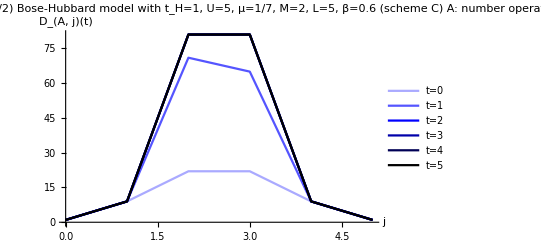

```mathematica
(* virtual bond dimension for 'A' operator *)
Partition[Import["../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>"_DXA.dat","Integer64"],Subscript[L, val]+1]
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(A, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t/2) A ⅇ^(-β H/2) ⅇ^(ⅈ H t/2)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DA_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

{{1,9,22,22,9,1},{1,9,28,32,9,1},{1,9,37,42,9,1},{1,9,45,57,9,1},{1,9,62,74,9,1},{1,9,77,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1},{1,9,81,81,9,1}}

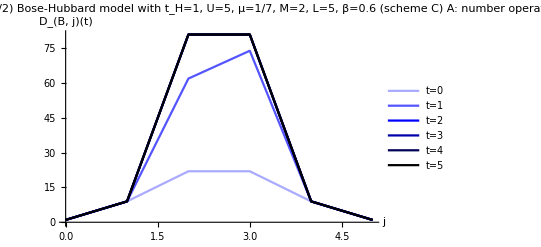

```mathematica
(* virtual bond dimension for 'B' operator *)
Partition[Import["../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>"_DXB.dat","Integer64"],Subscript[L, val]+1]
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(B, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(ⅈ H t/2) ⅇ^(-β H/2) B ⅇ^(-ⅈ H t/2)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DB_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

### Effective truncation weight

```mathematica
(* tolerance (truncation weight) for ⅇ^(-β H/2) *)
Partition[Import["../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>"_tol_eff_beta.dat","Real64"],Subscript[L, val]-1]
```

{{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10}}

```mathematica
(* tolerance (truncation weight) for ⅇ^(-ⅈ H t/2) A ⅇ^(-β H/2) ⅇ^(ⅈ H t/2) *)
Partition[Import["../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>"_tol_eff_A.dat","Real64"],Subscript[L, val]-1]
Dimensions[%]
```

{{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10}}

{20,4}

```mathematica
(* tolerance (truncation weight) for ⅇ^(ⅈ H t/2) ⅇ^(-β H/2) B ⅇ^(-ⅈ H t/2) *)
Partition[Import["../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>"_tol_eff_B.dat","Real64"],Subscript[L, val]-1]
Dimensions[%]
```

{{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10}}

{20,4}